((1+ⅇ^((√G Itp √Its L)/(√Cs √(Itp (Itp+Its)) √Ε))) √G √Its √(Itp (Itp+Its)) L-2 √Cs (-1+ⅇ^((√G Itp √Its L)/(√Cs √(Itp (Itp+Its)) √Ε))) (Itp+Its) √Ε)/(-(1+ⅇ^((√G Itp √Its L)/(√Cs √(Itp (Itp+Its)) √Ε))) √G √Its √(Itp (Itp+Its)) L+2 √Cs (-1+ⅇ^((√G Itp √Its L)/(√Cs √(Itp (Itp+Its)) √Ε))) Its √Ε)

1/(-(2 Its)/(Itp L)+(√G √Its √(Itp (Itp+Its)) Coth[(√G Itp √Its L)/(2 √Cs √(Itp (Itp+Its)) √Ε)])/(√Cs Itp √Ε))

((Itp+Its) ((1+ⅇ^((√G Itp √Its L)/(√Cs √(Itp (Itp+Its)) √Ε))) √G Itp √Its L-2 √Cs (-1+ⅇ^((√G Itp √Its L)/(√Cs √(Itp (Itp+Its)) √Ε))) √(Itp (Itp+Its)) √Ε))/((1+ⅇ^((√G Itp √Its L)/(√Cs √(Itp (Itp+Its)) √Ε))) √G Itp √Its (Itp+Its) L-2 √Cs (-1+ⅇ^((√G Itp √Its L)/(√Cs √(Itp (Itp+Its)) √Ε))) Its √(Itp (Itp+Its)) √Ε)

1/(-(2 Its)/(Itp L)+(√G √Its √(Itp (Itp+Its)) Coth[(√G Itp √Its L)/(2 √Cs √(Itp (Itp+Its)) √Ε)])/(√Cs Itp √Ε))

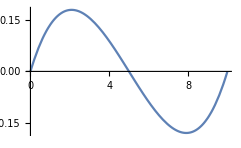

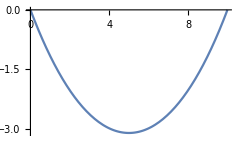

```mathematica
(* ΑΝΟΜΟΙΟΜΟΡΦΗ ΣΤΡΕΨΗ ΜΕ ΔΕΥΤΕΡΟΓΕΝΕΙΣ ΣΤΡΕΠΤΙΚΕΣ ΠΑΡΑΜΟΡΦΩΣΕΙΣ *)
(* Υπολογισμός μητρώου δυσκαμψίας και επικόμβιων φορτίων από τις αρχικές συνθήκες *)
Clear[θx,θxp,mt,mw,Mt,Mw,x]
mt[x_]:=0;
mw[x_]:=1;
sol=DSolve[{
mt[x]==-G (Itp+Its) θx''[x]+G Its θxp''[x],
mw[x]==Ε Cs θxp'''[x]-G Its(θxp'[x]-θx'[x])
},{θx[x],θxp[x]},x];
θx[x_]:=Evaluate[θx[x]/.sol⟦1⟧]
θxp[x_]:=Evaluate[θxp[x]/.sol⟦1⟧]
(* H σταθερά C[3] εξαφανίζεται επειδή χρησιμοποιούμε την παράγωγο της θtp και όχι την ίδια *)
sol=Solve[{θx[0]==0,θxp'[0]==0,θx[L]==0,θxp'[L]==0},{C[1],C[2],C[4],C[5]}];
θx[x_]:=Evaluate[θx[x]/.sol⟦1⟧]
θxp[x_]:=Evaluate[θxp[x]/.sol⟦1⟧]
Mt[x_]:=-G Itp θx'[x]+G Its(θxp'[x]-θx'[x])
Mw[x_]:=-Ε Cs θxp''[x]
k2=FullSimplify[Mt[0]]
k4=FullSimplify[Mw[0]]
k6=FullSimplify[-Mt[L]]
k8=FullSimplify[-Mw[L]]
Plot[θx[x]/.{L->10,G->1,Itp->1,Its->0.1,Cs->1,Ε->3},{x,0,10}]
Plot[θxp'[x]/.{L->10,G->1,Itp->1,Its->0.1,Cs->1,Ε->3},{x,0,10}]
(* ΠΡΟΣΟΧΗ!!! Οι επικόμβιες δυνάμεις που προκύπτουν από το κατανεμημένο έχουν αντίθετο πρόσημο F0'=-F0. Η μητρωϊκή σχέση είναι F=K.X-F0 *)
```